```mathematica
X={{1,0.4739269923},{2,0.5933056282},{3,0.6611677883},{4,0.7090386832},{5,0.7460324066},{6,0.7761436978},{7,0.8014938306},{8,0.8233464045},{9,0.8425154740},{10,0.8595564028},{11,0.8748650432},{12,0.8887335001},{13,0.9013834638},{14,0.9129871433},{15,0.9236809525},{16,0.9335747630},{17,0.9427583450},{18,0.9513059676},{19,0.9592797447},{20,0.9667321303},{21,0.9737077992},{22,0.9802450877},{23,0.9863771164},{24,0.9921326718},{25,0.9975369085},{26,1.0026119118},{27,1.0073771539},{28,1.0118498668},{29,1.0160453518},{30,1.0199772341},{31,1.0236576728},{32,1.0270975405},{33,1.0303065735},{34,1.0332934979},{35,1.0360661398},{36,1.0386315168},{37,1.0409959163},{38,1.0431649646},{39,1.0451436835},{40,1.0469365424},{41,1.0485475001},{42,1.0499800412},{43,1.0512372081},{44,1.0523216281},{45,1.0532355362},{46,1.0539807933},{47,1.0545589018},{48,1.0549710180},{49,1.0552179613},{50,1.0553002209},{51,1.0552179593},{52,1.0549710141},{53,1.0545588960},{54,1.0539807857},{55,1.0532355268},{56,1.0523216171},{57,1.0512371957},{58,1.0499800277},{59,1.0485474858},{60,1.0469365273},{61,1.0451436671},{62,1.0431649468},{63,1.0409958978},{64,1.0386314972},{65,1.0360661185},{66,1.0332934754},{67,1.0303065500},{68,1.0270975157},{69,1.0236576462},{70,1.0199772056},{71,1.0160453215},{72,1.0118498350},{73,1.0073771214},{74,1.0026118791},{75,0.9975368746},{76,0.9921326365},{77,0.9863770793},{78,0.9802450480},{79,0.9737077576},{80,0.9667320864},{81,0.9592796983},{82,0.9513059191},{83,0.9427582930},{84,0.9335747071},{85,0.9236808935},{86,0.9129870816},{87,0.9013834016},{88,0.8887334386},{89,0.8748649842},{90,0.8595563426},{91,0.8425154105},{92,0.8233463364},{93,0.8014937592},{94,0.7761436260},{95,0.7460323333},{96,0.7090386072},{97,0.6611677227},{98,0.5933055894},{99,0.4739269646}};
```

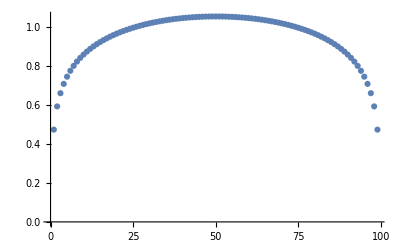

```mathematica
ListPlot[X]
```

```mathematica
XX=Select[X,#⟦1⟧> 10 && #⟦1⟧<90 &];
```

```mathematica
model= c/3 Log[Sin[Pi x/100]]+d;
```

```mathematica
fit=FindFit[XX,model,{c,d},x]
```

{c→0.500029,d→1.0553}

```mathematica
modelf=Function[{x},Evaluate[model/.fit]];
```

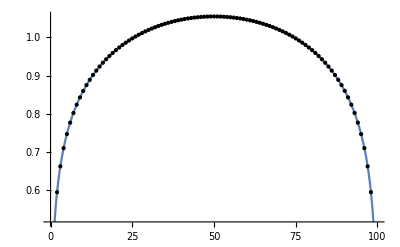

```mathematica
Plot[modelf[x],{x,0,100},Epilog->Map[Point,X]]
```